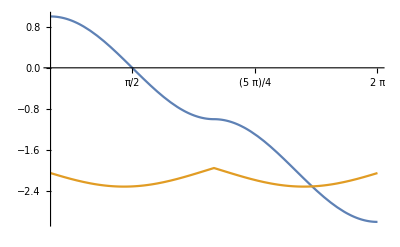

```mathematica
gamma[x_]:=If[x<π,Cos[x],-2-Cos[x]];
a=1.1π;
diff[x_]:=If[x<π,gamma[x+a]-gamma[x],gamma[x]-gamma[x-a]];




Plot[{gamma[x],diff[x]},
{x,0,2π},
Ticks->{Range[-Pi,2Pi,Pi/4],Automatic}]
```